# Stellar structures exercises

## The Lane-Emden like equations for a completely degenerate matter

The Lane-Emden like equations for a completely degenerate matter is given by
	1/ξ^2 d/dξ(ξ^2 dθ/dξ)=-(θ^(3/2)(θ+2/f_c))^(3/2), θ(0)=1. θ'(0)=0

## #9

Problem statement
Show that for nonrelativistic densities, f_c<<1, the structure equation reduces to that of a polytrope with n=3/2. By numerically integrating the equation, show that the mass and radius of the star scales with the central density ρ_c as

	M=0.496028(ρ_c/(10^9 kg/m^3))^(1/2)M_⊙, 		R=1.12160 x 10^7((10^9 kg/m^3)/ρ_c)^(1/6) meters

Solution
For f_c<<1, the second term in the RHS dominates and the Lane-Emden like equations become
	1/ξ^2 d/dξ(ξ^2 dθ/dξ)=-((2θ)/f_c)^(3/2)
Re scaling so that
	ξ=f_c^(3/4)y
we obtain
	1/y^2 d/dy(y^2 dθ/dy)=-(2θ)^(3/2)
which is a Lane-Emden equation for n=3/2.

```mathematica
1/y^2 D[(y^2 D[θ[y], y]), y]//Expand
```

(2 θ'[y])/y+θ''[y]

```mathematica
LEeqn=θ''[y]+2 θ'[y]/y==-(2θ[y])^(3/2);
```

This ODE is singular at y=0. To get an idea of how it looks like, we assume that θ(0.0001)=1, and θ'(0.0001)=0 and we numerically integrate it (the more rigorous way is to do an asymptotic expansion about y=0).

```mathematica
LEsol=NDSolve[{LEeqn,θ[0.0001]==1,θ'[0.0001]==0},θ,{y,0.0001,10}];
```

```mathematica
Clear[θ];
th[y_]=Re[θ[y]/.First@LEsol];
```

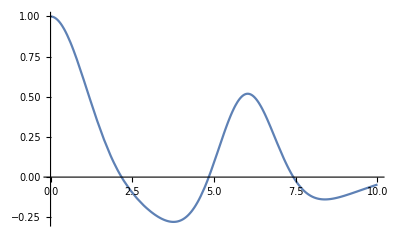

```mathematica
Plot[th[y],{y,0.0001,10}]
```

```mathematica
FindRoot[th[y],{y,2}]
```

{y→2.17253}

This corresponds to ξ_1=2.17253 f_c^(3/4).
This corresponds to a radius
	R=ξ_1 r_0=2.17253 f_c^(3/4)r_0=((8.43954 × 10^6)/f_c^(1/4)) meters
For f_c<<1, we have
	 f_c≃1/2 x_c^2=1/2(ρ_c/ρ_0)^(2/3); ρ_0=1.94787 × 10^9kg/m^3.
With this, we have
	R=2^(1/4)ρ_0^(1/6)((8.43954 × 10^6)/ρ_c^(1/6)) meters=1.1216 × 10^7((10^9 kg/m^3)/ρ_c)^(1/6) meters

For the mass relation, we have
	μ(ξ)=-ξ^2 dθ/dξ
And with our transformation to the variable y
	μ(y)=-f_c^(3/4)y^2 dθ/dy

```mathematica
Clear[dth];
dth[y_]=Re[θ'[y]/.First@LEsol];
```

```mathematica
2.17253^2*dth[2.17253]
```

-1.61379

Then we have
	M=μ(y_1)m_0=1.61379 f_c^(3/4)m_0≃1.16428 f_c^(3/4) M_⊙=0.496027(ρ_c/(10^9 kg/m^3))^(1/2)M_⊙

## #10

Problem statement
Show that for ultrarelativistic densities, f_c>>1, the structure equation reduces to that of a polytrope with n=3. By numerically integrating the equation, show that the mass and radius of the star scales with the central density ρ_c as
	M=1.45607 M_⊙, 	R=3.34598 x 10^7((10^9 kg/m^3)/ρ_c)^(1/3) meters

Solution
For f_c>>1, the first term in the RHS dominates and the Lane-Emden like equations become
1/ξ^2 d/dξ(ξ^2 dθ/dξ)=-θ^3.

```mathematica
LE2eqn=θ''[x]+2 θ'[x]/x==-θ[x]^3;
```

Similar to #9, we numerically solve this by assuming that θ(0.0001)=1.

```mathematica
LE2sol=NDSolve[{LE2eqn,θ[0.0001]==1,θ'[0.0001]==0},θ,{x,0.0001,10}];
```

```mathematica
Clear[θ]
```

```mathematica
th2[x_]=Re[θ[x]/.LE2sol];
dth2[x_]=Re[θ'[x]/.LE2sol];
```

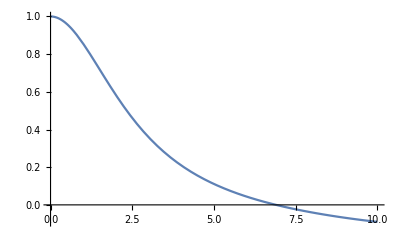

```mathematica
Plot[th2[x],{x,0.0001,10}]
```

```mathematica
FindRoot[th2[x],{x,6}]
```

{x→6.89685}

This corresponds to a radius of 
	R=ξ_1 r_0=6.89685 r_0=((26.7919×10^6)/f_c) meters.
But for f_c>>1, we have 
	f_c≃x_c=(ρ_c/ρ_0)^(1/3)=(ρ_c/(1.94787×10^9 kg/m^3))^(1/3)
so that
	R=1.94787^(1/3)((26.7919×10^6)/ρ_c^(1/3))(10^9 kg/m^3)^(1/3)meters=3.34598×10^7((10^9 kg/m^3)/ρ_c)^(1/3)meters.

For the mass, we have
	μ(θ)=-ξ^2 dθ/dξ
and
	M=μ(ξ_1)m_0.

```mathematica
-6.89685^2*dth2[6.89685]
```

{2.01824}

We have
	M=2.01824 m_0=1.45608 M_⊙.

## #11

Problem statement
Integrate the structure equations for different values of f_c to produce a sequence of {M(f_c),R(f_c)}. Plot M/M_⊙ vs f_c and R/(10^6 km) vs M/M_⊙. White dwarf populations cluster around a mass M=0.6 M_⊙. What f_c and ρ_c does this mass correspond to? What would you expect to be the typical radii of these white dwarfs?

Solution
Now we look at the Lane-Emden like equations for arbitrary f_c.

```mathematica
LE3eqn[fc_]:=θ''[x]+2 θ'[x]/x==-θ[x]^(3/2)(θ[x]+2/fc)^(3/2);
```

We need a function to obtain the first root (ξ_1) of the Lane-Emden like equation above.

```mathematica
(*Nagloloko to for very small fc*)
getSolLE3[fc_]:=Module[{root,sol},
root=0;
sol=NDSolve[{LE3eqn[fc],θ[0.0001]== 1,θ'[0.0001]== 0,WhenEvent[Re[θ[x]]==0,root=x;"StopIntegration"]},θ,{x,0.0001,20}];
Return[{root,First@sol}]
];
```

We construct a function that obtains M and R values

```mathematica
(*Obtains (R,M) data point for a given fc value. R is in units of km, while M is in units of Subscript[M, sun]*)
getMR[fc_]:=Module[{x1,R,sol,dth,M},
sol=getSolLE3[fc];
x1=First@sol;
R=x1*(3.88466/fc)*10^3;
dth[x_]=Re[θ'[x]/.Last@sol];
M=-x1^2*dth[x1]*0.721459;
Return[{R,M}]
]
```

```mathematica
fcvalues=Range[0.1,10,0.01]~Join~Range[11,1000];
```

```mathematica
MRdata=Table[pt=getMR[i];{pt⟦1⟧,pt⟦2⟧},{i,fcvalues}];//AbsoluteTiming
```

{7.94973,Null}

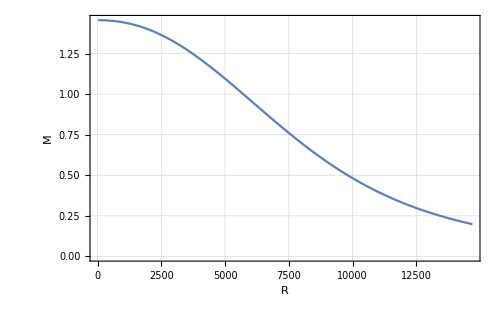

```mathematica
ListPlot[MRdata,PlotRange->All,Joined->True,GridLines->Automatic,Frame-> True,LabelStyle->Directive[Bold, 14],FrameLabel->{"R","M"},ImageSize->500]
```

I try to go to lower values of fc

```mathematica
fcvalues2=Range[0.001,10,0.001]~Join~Range[11,1000];
```

```mathematica
MRdata2=Table[pt=getMR[i];{pt⟦1⟧,pt⟦2⟧},{i,fcvalues2}];//AbsoluteTiming
```

{45.4236,Null}

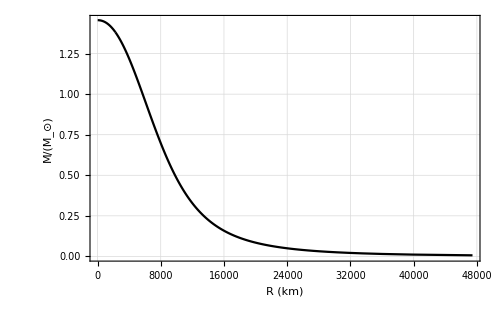

```mathematica
ListPlot[MRdata2,Joined->True,GridLines->Automatic,PlotStyle->Black,PlotRange->All,Frame-> True,LabelStyle->Directive[Bold, 14],FrameLabel->{Style["R (km)",16],Style["M/(M_⊙)",16]},RotateLabel->False,ImageSize->500]
```

```mathematica
Length[fcvalues2]
```

10990

```mathematica
Mfcdata2=Table[{fcvalues2⟦i⟧,Last@MRdata2⟦i⟧},{i,10990}];
```

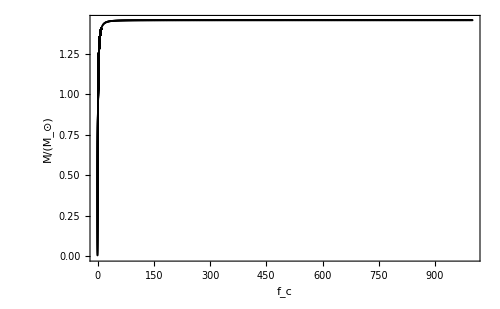

```mathematica
ListPlot[Mfcdata2,PlotStyle->Black,PlotRange->All,Frame-> True,LabelStyle->Directive[Bold, 14],FrameLabel->{Style["f_c",16],Style["M/(M_⊙)",16]},RotateLabel->False,ImageSize->500]
```

```mathematica
getMR[0.55]
```

{8826.34,0.601555}

For M=0.6 M_⊙, we have an f_c≃0.55 and a radius R≃8800 km.

```mathematica
Solve[0.55== √(1+xc^2)-1,xc]
```

{{xc→-1.18427},{xc→1.18427}}

```mathematica
xc=xc/.Last@%
```

1.18427

```mathematica
ρ0=1.94787; (*×10^9 kg/m^3*)
ρc=ρ0*xc^3 (*×10^9 kg/m^3*)
```

3.2353

This corresponds to a central density ρ_c≃3.2353×10^9 kg/m^3. For comparison, the density of Uranium is ρ_U=19.1×10^3 kg/m^3. White dwarfs are about 1 million times more dense than Uranium.